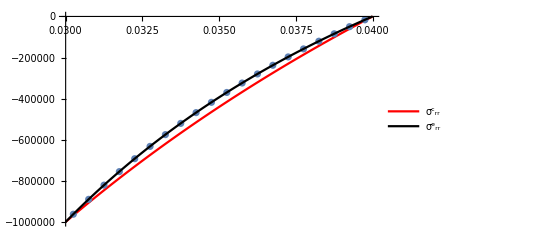

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
numSolution=ReadList["pols2.txt", {Number, Number}];
settings = ReadList["polsSettings2.txt",Number];
h =settings[[1]];a =settings[[2]];b =settings[[3]];
Pa =settings[[4]];
Pb=settings[[5]];
e=settings[[6]];
nu=settings[[7]];
T = settings[[8]];
M=settings[[9]];
n =3;
p=Pa;
r1=a;r2=b;
exactSigmaRR[r_]:=(p r1^(2/n))/(r2^(2/n)-r1^(2/n))(1- r2^(2/n)/r^(2/n))
sigmaRRPlot=Plot[exactSigmaRR[r],{r,a,b}];
exactSigmaFF[r_]:=(p r1^(2/n))/(r2^(2/n)-r1^(2/n))(1+(2-n)/n r2^(2/n)/r^(2/n))
sigmaFFPlot=Plot[exactSigmaFF[r],{r,a,b},PlotStyle->{Red},PlotLegends->{"(σ^c)_ϕϕ"}];
sigmaRRPlot=Plot[exactSigmaRR[r],{r,a,b},PlotStyle->{Red},PlotLegends->{"(σ^c)_rr"}];

exactSigmaFFUpr[h_]:= (Pa  a^2-Pb  b^2)/(b^2-a^2)+ (a^2 b^2)/h^2 * (Pa -Pb)/(b^2-a^2);
sigmaFFPlotUpr=Plot[exactSigmaFFUpr[r],{r,a,b},PlotStyle->Black,PlotLegends->{"(σ^e)_ϕϕ"}];
exactSigmaRRUpr[h_]:= (Pa  a^2-Pb  b^2)/(b^2-a^2)- (a^2 b^2)/h^2 * (Pa -Pb)/(b^2-a^2);
sigmaRRPlotUpr=Plot[exactSigmaRRUpr[r],{r,a,b},PlotStyle->Black,PlotLegends->{"(σ^e)_rr"}];
numSigmaFF=Import["sigmaFFPols2.txt","Table"];
numTableFF={};
numSigmaRR=Import["sigmaRRPols2.txt","Table"];
numTableRR={};
For[i =1,i<Length[numSigmaFF],i++,
r=a-h;numFF={};numRR={};
For[k=0,k<Length[numSigmaFF[[i]]],k++,
r+=2*h;(*подумать*)
numFF=Append[numFF,{r,numSigmaFF[[i]][[k+1]]}];
numRR=Append[numRR,{r,numSigmaRR[[i]][[k+1]]}];
];
numTableRR=Append[numTableRR,numRR];
numTableFF=Append[numTableFF,numFF];
]
Show[sigmaRRPlot,ListPlot[numTableRR[[1]]],sigmaRRPlotUpr]
```

```mathematica
gif=Animate[
Show[sigmaFFPlot,ListPlot[numTableFF[[i]]],sigmaFFPlotUpr],{i,1,M-1,1}]
Export["SigmaFF.gif",gif]
```

SigmaFF.gif

```mathematica
gifRR=Animate[
Show[sigmaRRPlot,ListPlot[numTableRR[[i]]],sigmaRRPlotUpr],{i,1,M-1,1}]
Export["SigmaRR.gif",gifRR]
```

SigmaRR.gif